```mathematica
BesselI[0,0]
Integrate[Cos[x y],{x,0,1},{y,0,x}]
```

1

SinIntegral[1]/2

```mathematica
-BesselI[0,r]BesselK[0,R]HeavisideTheta[R-r]-BesselI[0,R]BesselK[0,r]HeavisideTheta[r-R]
```

-BesselI[0,R] BesselK[0,r] HeavisideTheta[r-R]-BesselI[0,r] BesselK[0,R] HeavisideTheta[-r+R]

```mathematica
(1.878*10^8)/(5*5^2*10^(-18)*(2*Pi)^(1.5))
```

9.53928×10^22

```mathematica
Cos[X-x](-BesselI[0,R] BesselK[0,r] HeavisideTheta[r-R]-BesselI[0,r] BesselK[0,R] HeavisideTheta[-r+R])((1.878*10^8)/(5*5^2*10^(-18)*(2*Pi)^(1.5)) Exp[-R^2/(2*(5*10^(-6))^2)-x^2/(2*(5*10^(-6))^2)])R
```

9.53928×10^22 ⅇ^(-20000000000 x^2-20000000000 y^2)

```mathematica
kp=1.83*10^5;
e= 1.60217662*10^(-19);
epsilon0:= 8.85*10^(-12);
r=0;
y2[X_]:=-((e *kp^2)/(epsilon0))Integrate[Cos[kp(X-x)](-BesselK[0,kp*R] )((1.878*10^8)/(5*(8.5/3)^2*10^(-18)*(2*Pi)^(1.5)) R*Exp[-R^2/(2*((8.5/3)*10^(-6))^2)-(x)^2/(2*(5*10^(-6))^2)]),{x,-Infinity,X},{R,0,Infinity}]

y2[0 *10 ^(-6)]
```

Indeterminate

```mathematica
kp=183414;
e= 1.60217662*10^(-19);
epsilon0= 8.854187817*10^(-12);
r=0;
y[X_]:=-((e *kp^2)/(epsilon0))Integrate[Cos[kp(X-x)](-BesselK[0,kp*R] )((1.87*10^6)/(5*5^2*10^(-18)*(2*Pi)^(1.5)) R*Exp[-R^2/(2*(5*10^(-6))^2)-(x)^2/(2*(5*10^(-6))^2)]),{x,-Infinity,X},{R,0,Infinity}]


y[0 *10^(-6)]
```

3.031×10^7

```mathematica
points=Table[{x,y[x]},{x,Range[0*10^(-6),65*10^(-6),1*10^(-6)]}];
```

Integrate::ilim: Invalid integration variable or limit(s) in {0,-∞,0}.

Integrate::ilim: Invalid integration variable or limit(s) in {1/1000000,-∞,1/1000000}.

Integrate::ilim: Invalid integration variable or limit(s) in {1/500000,-∞,1/500000}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

```mathematica
RealDigits[5.193512495014662*^9]
```

{{5,1,9,3,5,1,2,4,9,5,0,1,4,6,6,2},10}

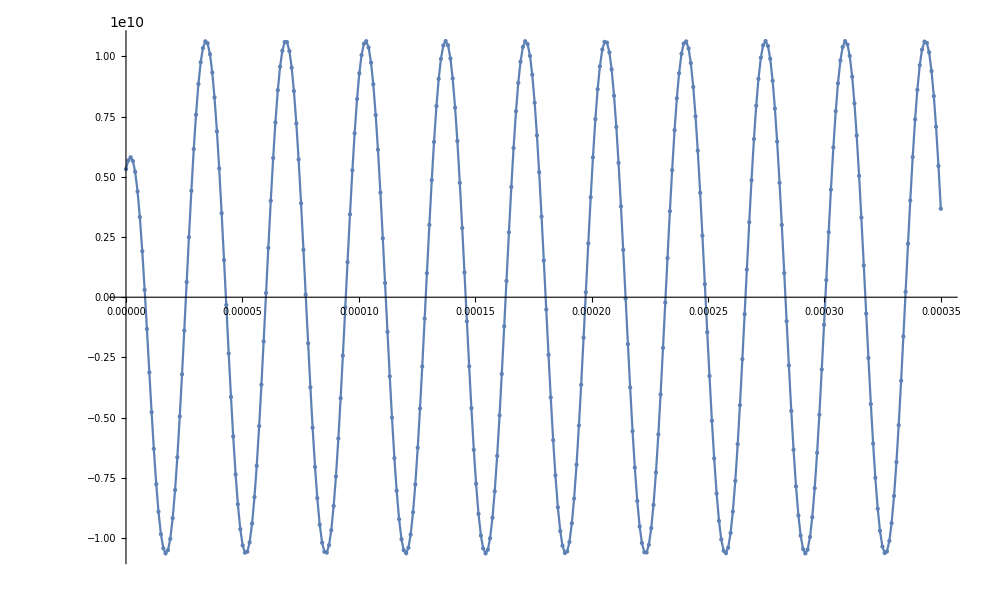

```mathematica
fig=Plot[y[a],{a,0*10 ^(-6),350*10 ^(-6)},Mesh->All,MaxRecursion->0,PlotPoints->350]
```

```mathematica
Do[Print[Re[y[i*10^(-6)]]],{i,0,68,1}]
```

3.031×10^7

3.23854×10^7

3.30893×10^7

3.21459×10^7

2.93944×10^7

2.48101×10^7

1.85086×10^7

1.07327×10^7

1.82756×10^6

-7.79135×10^6

-1.76725×10^7

-2.73598×10^7

-3.64183×10^7

-4.44548×10^7

-5.11317×10^7

-5.61762×10^7

-5.93862×10^7

-6.06327×10^7

-5.98611×10^7

-5.70897×10^7

-5.24074×10^7

-4.59691×10^7

-3.79896×10^7

-2.87361×10^7

-1.85189×10^7

-7.68043×10^6

3.41563×10^6

1.43971×10^7

2.48956×10^7

3.45589×10^7

4.30629×10^7

5.01223×10^7

5.55003×10^7

5.90164×10^7

6.05527×10^7

6.00577×10^7

5.7548×10^7

5.31077×10^7

4.68859×10^7

3.90912×10^7

2.99851×10^7

1.98732×10^7

9.09452×10^6

-1.98921×10^6

-1.30062×10^7

-2.35869×10^7

-3.33763×10^7

-4.20461×10^7

-4.93054×10^7

-5.49106×10^7

-5.86738×10^7

-6.04687×10^7

-6.02351×10^7

-5.79808×10^7

-5.37814×10^7

-4.77779×10^7

-4.01716×10^7

-3.12177×10^7

-2.12165×10^7

-1.05036×10^7

561679.

1.16081×10^7

2.22651×10^7

3.21752×10^7

4.10059×10^7

4.84611×10^7

5.42905×10^7

5.82987×10^7

6.03511×10^7

```mathematica
(1*10^4)/(50*10^2*10^(-18)*(2*Pi)^(1.5))
```

1.26987×10^17